```mathematica
ClearAll["Global`*"]
```

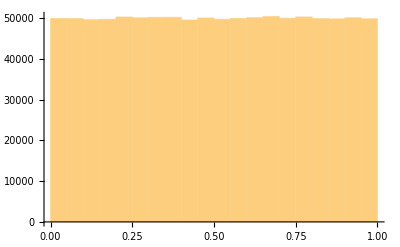

```mathematica
(*Veamos que RandomReal[] es uniforme*)
nmax = 10^6;
randlist = ConstantArray[0,nmax];
Do[
randlist[[j]] = RandomReal[];
,{j,1,Length[randlist]}]

Histogram[randlist, Automatic]
(*parece uniforme*)
```

Lista completa

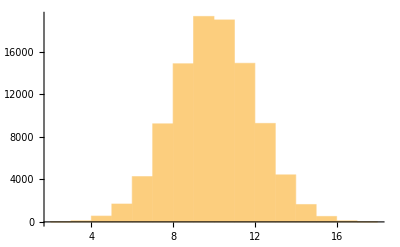

```mathematica
ClearAll["Global`*"]
ybar = 10;
sigma = 2;
Prob[y_]:=(E^((-(y- ybar )^2)/(2 sigma^2)))/(√(2 Pi)sigma)
ymin = ybar - 4 sigma;
ymax = ybar + 4 sigma;
Pmax = Prob[ybar]; (*el máximo está en y=ybar por simetría*)

nmax = 10^5; (*cantidad de elementos en la lista final prob_list*)
problist = ConstantArray[0,nmax];

jmax = 10*nmax; (*cantidad total de iteraciones que hace Do*)
n = 1;
Do[
(*genero y random*)
y = RandomReal[]*(ymax - ymin) + ymin;
(*genero x random*)
x = RandomReal[]*Pmax;
(*evalúo P(y) y comparo con x*)
If[x<Prob[y],problist[[n]]=y;n++]; (*condición de rechazo*)
If[n>nmax,Print["Lista completa"]; Break[]] (*si problist ya tiene nmax elementos, salí del Do*)
,{j,1,jmax}]

Histogram[problist]
(*parece una gaussiana*)
```